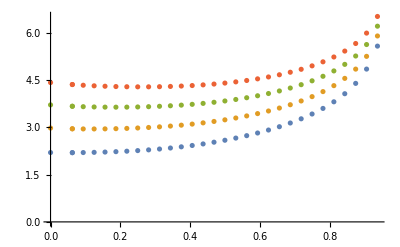

```mathematica
a={{0,2.199345},{0.062500,2.195900},{0.062500,2.195900},{0.093750,2.199482},{0.125000,2.205868},{0.156250,2.215057},{0.187500,2.227208},{0.218750,2.242576},{0.250000,2.261486},{0.281250,2.284318},{0.312500,2.311498},{0.343750,2.343476},{0.375000,2.380712},{0.406250,2.423641},{0.437500,2.472626},{0.468750,2.527939},{0.500000,2.589821},{0.531250,2.658637},{0.562500,2.734988},{0.593750,2.819698},{0.625000,2.913843},{0.656250,3.018848},{0.687500,3.136637},{0.718750,3.269857},{0.750000,3.422228},{0.781250,3.599175},{0.812500,3.809011},{0.843750,4.065408},{0.875000,4.393357},{0.906250,4.846924},{0.937500,5.575393}};
a2={{0,2.976460},{0.062500,2.952840},{0.062500,2.952840},{0.093750,2.948610},{0.125000,2.948033},{0.156250,2.950758},{0.187500,2.956688},{0.218750,2.965873},{0.250000,2.978463},{0.281250,2.994680},{0.312500,3.014799},{0.343750,3.039137},{0.375000,3.068048},{0.406250,3.101910},{0.437500,3.141130},{0.468750,3.186142},{0.500000,3.237420},{0.531250,3.295500},{0.562500,3.361008},{0.593750,3.434710},{0.625000,3.517567},{0.656250,3.610831},{0.687500,3.716168},{0.718750,3.835861},{0.750000,3.973127},{0.781250,4.132677},{0.812500,4.321754},{0.843750,4.552297},{0.875000,4.846141},{0.906250,5.250507},{0.937500,5.897239}};
a3={{0,3.711176},{0.062500,3.667642},{0.062500,3.667642},{0.093750,3.654407},{0.125000,3.645515},{0.156250,3.640387},{0.187500,3.638745},{0.218750,3.640488},{0.250000,3.645640},{0.281250,3.654313},{0.312500,3.666687},{0.343750,3.683002},{0.375000,3.703547},{0.406250,3.728658},{0.437500,3.758716},{0.468750,3.794152},{0.500000,3.835450},{0.531250,3.883161},{0.562500,3.937929},{0.593750,4.000516},{0.625000,4.071856},{0.656250,4.153128},{0.687500,4.245867},{0.718750,4.352141},{0.750000,4.474833},{0.781250,4.618142},{0.812500,4.788510},{0.843750,4.996544},{0.875000,5.261630},{0.906250,5.625697},{0.937500,6.207211}};
a4={{0,4.419583},{0.062500,4.356975},{0.062500,4.356975},{0.093750,4.334269},{0.125000,4.316441},{0.156250,4.302775},{0.187500,4.292862},{0.218750,4.286494},{0.250000,4.283601},{0.281250,4.284210},{0.312500,4.288429},{0.343750,4.296434},{0.375000,4.308460},{0.406250,4.324795},{0.437500,4.345783},{0.468750,4.371827},{0.500000,4.403388},{0.531250,4.441004},{0.562500,4.485303},{0.593750,4.537030},{0.625000,4.597091},{0.656250,4.666612},{0.687500,4.747040},{0.718750,4.840297},{0.750000,4.949034},{0.781250,5.077080},{0.812500,5.230270},{0.843750,5.418183},{0.875000,5.658282},{0.906250,5.988304},{0.937500,6.515934}};
ListPlot[{a,a2,a3,a4}]
```

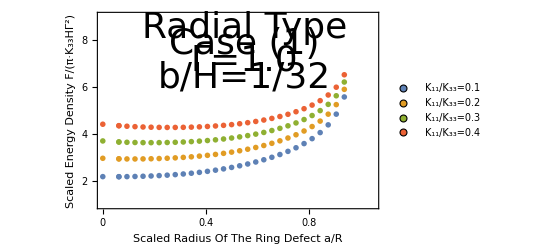

```mathematica
ListPlot[{a,a2,a3,a4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{2,4,6,8,10},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{1,9}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{0.55,8.5}],Text[Style["Case (1)",Directive[Black,36]],{0.55,7.8}],Text[Style["Γ=1.0",Directive[Black,36]],{0.55,7.1}],Text[Style["b/H=1/32",Directive[Black,36]],{0.55,6.4}]}]
```

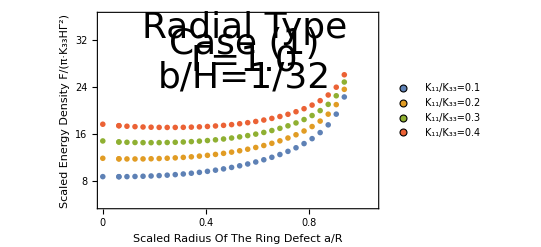

```mathematica
aa=a*Table[{1,4},{i,0,30}];
aa2=a2*Table[{1,4},{i,0,30}];
aa3=a3*Table[{1,4},{i,0,30}];
aa4=a4*Table[{1,4},{i,0,30}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{8,16,24,32,40},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{4,36}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{0.55,34}],Text[Style["Case (1)",Directive[Black,36]],{0.55,31.2}],Text[Style["Γ=1.0",Directive[Black,36]],{0.55,28.4}],Text[Style["b/H=1/32",Directive[Black,36]],{0.55,25.6}]}]
```